## sigma

```mathematica
Clear[sig,s,μ,B,v0];
sig[B_,μ_,v0_,{βintra11_,βintra33_,βinter_}]:=Block[{e=1,s,sm,sol0,sol2,matr,bc1,bc2,θ,τ1,τ2,kf1,ϕ=0,kf2,f1,f2,vvec1,vvec2,vmm1,vmm2,vdotk1,vdotk2,conteq,h1,h2,λ1,a1,b1,c1,d1,g1,λ2,a2,b2,c2,d2,g2,cost,θp,Dphase1,Dphase2,vz1,vz2,cs,zero1,zero2,ct1,ct2,ctsq1,ctsq2,hzero1,hzero2,hct1,hct2,hctsq1,hctsq2,hctcube1,hctcube2,ctcube1,ctcube2,ctfive1,ctfive2,ctsix1,ctsix2,ctquad1 ,ctquad2,colvec,mat,sol,sol1,Λ1,Λ2,s1,s2,int1,int2},
(* band 1 *)
s=1/2;sm=7/4;
kf1[θ_]=(μ+√(μ^2-2 B e sm v0^2 Cos[θ]))/(2 v0);(* -Graphics-*);
bc1[θ_]=-s/( kf1[θ])^2{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase1[θ_]=1 +e {0,0,B}.bc1[θ] (*-Graphics-*);
vvec1[θ_]=s v0{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm1[θ_]=(-  sm B e v0)/( kf1[θ])^2{Cos[ϕ] Sin[2θ],Sin[2θ] Sin[ϕ], Cos[2 θ]};
vdotk1[θ_]=v0 (s-(B e sm Cos[θ])/kf1[θ]^2) kf1[θ];
(* -Graphics-*)
h1[θ_]=1/Dphase1[θ]( s v0 Cos[θ]-(B e sm v0 Cos[2 θ])/kf1[θ]^2+ e B(bc1[θ].(vvec1[θ]+vmm1[θ])) );
(*****************)

(* band 2 *)
s=3/2;sm=3/4;
kf2[θ_]=(μ+√(μ^2-2 B e sm v0^2 Cos[θ]))/(2 v0);
bc2[θ_]=(- s)/( kf2[θ])^2{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase2[θ_]=1 +e {0,0,B}.bc2[θ] (*-Graphics-*);
vvec2[θ_]=s v0{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm2[θ_]=(-  sm B e v0)/kf2[θ]^2{Cos[ϕ] Sin[2θ],Sin[2θ] Sin[ϕ], Cos[2 θ]};
vdotk2[θ_]=v0 (s-(B e sm Cos[θ])/kf2[θ]^2) kf2[θ];
h2[θ_]=1/Dphase2[θ]( s v0 Cos[θ]-(B e sm v0 Cos[2 θ])/kf2[θ]^2+ e B(bc2[θ].(vvec2[θ]+vmm2[θ])) );

(* ***************************** *)

τ1[θ_]=((*(5-3 ctp^2)+(17 ctp-27 ctp^3) ct + (-3+9 ctp^2) ct^2+ 9 ctp (-3+5 ctp^2) ct^3 *)βintra11/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp](5-3 Cos[θp]^2),{θp,0,π}]+
(βintra11   Cos[θ])/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp](17-27 Cos[θp]^2),{θp,0,π}]+
(βintra11   Cos[θ]^2)/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp](-3+9 Cos[θp]^2),{θp,0,π}]+
(9 βintra11  Cos[θ]^3)/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp] (-3+5 Cos[θp]^2),{θp,0,π}]
(*********** (3+3 ctp^2)+ct(-3 ctp+9 ctp^3) +(3-9 ctp^2) ct^2+(9 ctp-15 ctp^3) ct^3************)+(3βinter)/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp](1+ Cos[θp]^2),{θp,0,π}]+(-3βinter Cos[θ])/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp] (1-3 Cos[θp]^2),{θp,0,π}]+(3βinter Cos[θ]^2)/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp](1-3 Cos[θp]^2) ,{θp,0,π}]+(3βinter Cos[θ]^3)/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp](3 -5 Cos[θp]^2) ,{θp,0,π}])^-1;
(**************) 

τ2[θ_]=((* (5-3 ctp^2)+(9 ctp-3 ctp^3) ct+(-3+9 ctp^2) ct^2+(-3 ctp+5 ctp^3) ct^3 *)βintra33/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp](5-3 Cos[θp]^2),{θp,0,π}]+
(3 βintra33  Cos[θ])/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp] (3-Cos[θp]^2),{θp,0,π}]+
(3βintra33  Cos[θ]^2)/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp](-1+3 Cos[θp]^2),{θp,0,π}]+
(βintra33  Cos[θ]^3)/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp] (-3+5 Cos[θp]^2),{θp,0,π}]+

(*****(3+3 ctp^2)+ct(-3 ctp+9 ctp^3) +(3-9 ctp^2) ct^2+(9 ctp-15 ctp^3) ct^3 ***************************)+(3βinter)/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp](1+ Cos[θp]^2),{θp,0,π}]+(-3βinter Cos[θ])/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp] (1-3 Cos[θp]^2),{θp,0,π}]+(3βinter Cos[θ]^2)/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp](1-3 Cos[θp]^2) ,{θp,0,π}]+(3βinter Cos[θ]^3)/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp](3 -5 Cos[θp]^2) ,{θp,0,π}])^-1;
(****************************)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
f2[θ_]=(Sin[θ] (kf2[θ])^3)/Abs[vdotk2[θ]] Dphase2[θ] τ2[θ];
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];
zero2=Quiet[NIntegrate [f2[θp],{θp,0,π}]];
ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ct2=Quiet[NIntegrate [f2[θp] Cos[θp],{θp,0,π}]];
ctsq1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
ctsq2=Quiet[NIntegrate [f2[θp] Cos[θp]^2,{θp,0,π}]];
ctcube1=Quiet[NIntegrate [f1[θp] Cos[θp]^3,{θp,0,π}]];
ctcube2 =Quiet[NIntegrate [f2[θp] Cos[θp]^3,{θp,0,π}]];
ctquad1 =Quiet[NIntegrate [f1[θp] Cos[θp]^4,{θp,0,π}]];
ctquad2 =Quiet[NIntegrate [f2[θp] Cos[θp]^4,{θp,0,π}]];
ctfive1=Quiet[NIntegrate [f1[θp] Cos[θp]^5,{θp,0,π}]];
ctfive2=Quiet[NIntegrate [f2[θp] Cos[θp]^5,{θp,0,π}]];
ctsix1=Quiet[NIntegrate [f1[θp] Cos[θp]^6,{θp,0,π}]];
ctsix2=Quiet[NIntegrate [f2[θp] Cos[θp]^6,{θp,0,π}]];

hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hzero2=Quiet[NIntegrate [f2[θp]h2[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];
hct2=Quiet[NIntegrate [f2[θp]h2[θp]Cos[θp],{θp,0,π}]];
hctsq1=Quiet[NIntegrate [f1[θp]h1[θp] Cos[θp]^2,{θp,0,π}]];
hctsq2=Quiet[NIntegrate [f2[θp]h2[θp] Cos[θp]^2,{θp,0,π}]];
hctcube1=Quiet[NIntegrate [f1[θp]h1[θp] Cos[θp]^3,{θp,0,π}]];
hctcube2=Quiet[NIntegrate [f2[θp]h2[θp] Cos[θp]^3,{θp,0,π}]];


colvec=({{3 hctsq2 βinter+3 hzero2 βinter-3 hctsq1 βintra11+5 hzero1 βintra11}, {-3 hct2 βinter+9 hctcube2 βinter+17 hct1 βintra11-27 hctcube1 βintra11}, {-9 hctsq2 βinter+3 hzero2 βinter+9 hctsq1 βintra11-3 hzero1 βintra11}, {9 hct2 βinter-15 hctcube2 βinter-27 hct1 βintra11+45 hctcube1 βintra11}, {3 hctsq1 βinter+3 hzero1 βinter-3 hctsq2 βintra33+5 hzero2 βintra33}, {-3 hct1 βinter+9 hctcube1 βinter+9 hct2 βintra33-3 hctcube2 βintra33}, {-9 hctsq1 βinter+3 hzero1 βinter+9 hctsq2 βintra33-3 hzero2 βintra33}, {9 hct1 βinter-15 hctcube1 βinter-3 hct2 βintra33+5 hctcube2 βintra33}});
mat=({{1+3 ctsq1 βintra11-5 zero1 βintra11, -5 ct1 βintra11+3 ctcube1 βintra11, 3 ctquad1 βintra11-5 ctsq1 βintra11, -5 ctcube1 βintra11+3 ctfive1 βintra11, -3 ctsq2 βinter-3 zero2 βinter, -3 ct2 βinter-3 ctcube2 βinter, -3 ctquad2 βinter-3 ctsq2 βinter, -3 ctcube2 βinter-3 ctfive2 βinter}, {-17 ct1 βintra11+27 ctcube1 βintra11, 1+27 ctquad1 βintra11-17 ctsq1 βintra11, -17 ctcube1 βintra11+27 ctfive1 βintra11, -17 ctquad1 βintra11+27 ctsix1 βintra11, 3 ct2 βinter-9 ctcube2 βinter, -9 ctquad2 βinter+3 ctsq2 βinter, 3 ctcube2 βinter-9 ctfive2 βinter, 3 ctquad2 βinter-9 ctsix2 βinter}, {-9 ctsq1 βintra11+3 zero1 βintra11, 3 ct1 βintra11-9 ctcube1 βintra11, 1-9 ctquad1 βintra11+3 ctsq1 βintra11, 3 ctcube1 βintra11-9 ctfive1 βintra11, 9 ctsq2 βinter-3 zero2 βinter, -3 ct2 βinter+9 ctcube2 βinter, 9 ctquad2 βinter-3 ctsq2 βinter, -3 ctcube2 βinter+9 ctfive2 βinter}, {27 ct1 βintra11-45 ctcube1 βintra11, -45 ctquad1 βintra11+27 ctsq1 βintra11, 27 ctcube1 βintra11-45 ctfive1 βintra11, 1+27 ctquad1 βintra11-45 ctsix1 βintra11, -9 ct2 βinter+15 ctcube2 βinter, 15 ctquad2 βinter-9 ctsq2 βinter, -9 ctcube2 βinter+15 ctfive2 βinter, -9 ctquad2 βinter+15 ctsix2 βinter}, {-3 ctsq1 βinter-3 zero1 βinter, -3 ct1 βinter-3 ctcube1 βinter, -3 ctquad1 βinter-3 ctsq1 βinter, -3 ctcube1 βinter-3 ctfive1 βinter, 1+3 ctsq2 βintra33-5 zero2 βintra33, -5 ct2 βintra33+3 ctcube2 βintra33, 3 ctquad2 βintra33-5 ctsq2 βintra33, -5 ctcube2 βintra33+3 ctfive2 βintra33}, {3 ct1 βinter-9 ctcube1 βinter, -9 ctquad1 βinter+3 ctsq1 βinter, 3 ctcube1 βinter-9 ctfive1 βinter, 3 ctquad1 βinter-9 ctsix1 βinter, -9 ct2 βintra33+3 ctcube2 βintra33, 1+3 ctquad2 βintra33-9 ctsq2 βintra33, -9 ctcube2 βintra33+3 ctfive2 βintra33, -9 ctquad2 βintra33+3 ctsix2 βintra33}, {9 ctsq1 βinter-3 zero1 βinter, -3 ct1 βinter+9 ctcube1 βinter, 9 ctquad1 βinter-3 ctsq1 βinter, -3 ctcube1 βinter+9 ctfive1 βinter, -9 ctsq2 βintra33+3 zero2 βintra33, 3 ct2 βintra33-9 ctcube2 βintra33, 1-9 ctquad2 βintra33+3 ctsq2 βintra33, 3 ctcube2 βintra33-9 ctfive2 βintra33}, {-9 ct1 βinter+15 ctcube1 βinter, 15 ctquad1 βinter-9 ctsq1 βinter, -9 ctcube1 βinter+15 ctfive1 βinter, -9 ctquad1 βinter+15 ctsix1 βinter, 3 ct2 βintra33-5 ctcube2 βintra33, -5 ctquad2 βintra33+3 ctsq2 βintra33, 3 ctcube2 βintra33-5 ctfive2 βintra33, 1+3 ctquad2 βintra33-5 ctsix2 βintra33}});
matr=mat.{λ1,a1,b1,c1,λ2,a2,b2,c2};(* λ1 - h1+  a1 ct+b1 ct^2+c1  ct^3 *)
cs=(λ1 zero1-hzero1+a1 ct1+b1 ctsq1+c1 ctcube1)+(λ2 zero2-hzero2+a2 ct2+b2 ctsq2+c2 ctcube2);
(*sol0=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,matr[[3]]+colvec[[3]]==0,matr[[4]]+colvec[[4]]==0,matr[[5]]+colvec[[5]]==0,matr[[6]]+colvec[[6]]==0,matr[[7]]+colvec[[7]]==0,matr[[8]]+colvec[[8]]==0,cs==0},{λ1,a1,b1,c1,λ2,a2,b2,c2}],1];

sol1=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,matr[[3]]+colvec[[3]]==0,matr[[4]]+colvec[[4]]==0,matr[[5]]+colvec[[5]]==0,matr[[6]]+colvec[[6]]==0,matr[[7]]+colvec[[7]]==0,matr[[8]]+colvec[[8]]==0},{λ1,a1,b1,c1,λ2,a2,b2,c2}],1];*)

sol2=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,matr[[4]]+colvec[[4]]==0,matr[[5]]+colvec[[5]]==0,matr[[6]]+colvec[[6]]==0,matr[[7]]+colvec[[7]]==0,matr[[8]]+colvec[[8]]==0,cs==0},{λ1,a1,b1,c1,λ2,a2,b2,c2}],1];

sol=sol2;
Λ1[θ_]=(λ1-h1[θ]+a1 Cos[θ]+b1 Cos[θ]^2+c1  Cos[θ]^3)/.sol;
int1[θ_]=-f1[θ]h1[θ]Λ1[θ];
s1=NIntegrate[int1[θ],{θ,0,π}];

Λ2[θ_]=(λ2-h2[θ]+a2 Cos[θ]+b2 Cos[θ]^2+c2  Cos[θ]^3)/.sol;
int2[θ_]=-f2[θ]h2[θ]Λ2[θ];
s2=NIntegrate[int2[θ],{θ,0,π}];
{μ,s1,s2,s1+s2}
];
```

## sigma at B=0

```mathematica
Clear[sig0,s,μ,B,v0];
sig0[μ_,v0_,{βintra11_,βintra33_,βinter_}]:=Block[{e=1,B=0,s,sm,sol0,sol2,matr,bc1,bc2,θ,τ1,τ2,kf1,ϕ=0,kf2,f1,f2,vvec1,vvec2,vmm1,vmm2,vdotk1,vdotk2,conteq,h1,h2,λ1,a1,b1,c1,d1,g1,λ2,a2,b2,c2,d2,g2,cost,θp,Dphase1,Dphase2,vz1,vz2,cs,zero1,zero2,ct1,ct2,ctsq1,ctsq2,hzero1,hzero2,hct1,hct2,hctsq1,hctsq2,hctcube1,hctcube2,ctcube1,ctcube2,ctfive1,ctfive2,ctsix1,ctsix2,ctquad1 ,ctquad2,colvec,mat,sol,sol1,Λ1,Λ2,s1,s2,int1,int2},
(* band 1 *)
s=1/2;sm=7/4;
kf1[θ_]=μ/v0;
bc1[θ_]=-s/( kf1[θ])^2{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase1[θ_]=1;
vvec1[θ_]=s v0{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm1[θ_]={0,0,0};
vdotk1[θ_]=v0 s kf1[θ];
h1[θ_]=1/Dphase1[θ]( s v0 Cos[θ] );
(*****************)

(* band 2 *)
s=3/2;sm=3/4;
kf2[θ_]=μ/v0;
bc2[θ_]=(- s)/( kf2[θ])^2{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase2[θ_]=1 ;
vvec2[θ_]=s v0{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm2[θ_]={0,0,0};
vdotk2[θ_]=v0 s kf2[θ];
h2[θ_]=(s v0 Cos[θ])/Dphase2[θ];

(* ***************************** *)

τ1[θ_]=((*(5-3 ctp^2)+(17 ctp-27 ctp^3) ct + (-3+9 ctp^2) ct^2+ 9 ctp (-3+5 ctp^2) ct^3 *)βintra11/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp](5-3 Cos[θp]^2),{θp,0,π}]+
(βintra11   Cos[θ])/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp](17-27 Cos[θp]^2),{θp,0,π}]+
(βintra11   Cos[θ]^2)/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp](-3+9 Cos[θp]^2),{θp,0,π}]+
(9 βintra11  Cos[θ]^3)/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp] (-3+5 Cos[θp]^2),{θp,0,π}]
(*********** (3+3 ctp^2)+ct(-3 ctp+9 ctp^3) +(3-9 ctp^2) ct^2+(9 ctp-15 ctp^3) ct^3************)+(3βinter)/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp](1+ Cos[θp]^2),{θp,0,π}]+(-3βinter Cos[θ])/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp] (1-3 Cos[θp]^2),{θp,0,π}]+(3βinter Cos[θ]^2)/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp](1-3 Cos[θp]^2) ,{θp,0,π}]+(3βinter Cos[θ]^3)/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp](3 -5 Cos[θp]^2) ,{θp,0,π}])^-1;
(**************) 

τ2[θ_]=((* (5-3 ctp^2)+(9 ctp-3 ctp^3) ct+(-3+9 ctp^2) ct^2+(-3 ctp+5 ctp^3) ct^3 *)βintra33/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp](5-3 Cos[θp]^2),{θp,0,π}]+
(3 βintra33  Cos[θ])/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp] (3-Cos[θp]^2),{θp,0,π}]+
(3βintra33  Cos[θ]^2)/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp](-1+3 Cos[θp]^2),{θp,0,π}]+
(βintra33  Cos[θ]^3)/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp] (-3+5 Cos[θp]^2),{θp,0,π}]+

(*****(3+3 ctp^2)+ct(-3 ctp+9 ctp^3) +(3-9 ctp^2) ct^2+(9 ctp-15 ctp^3) ct^3 ***************************)+(3βinter)/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp](1+ Cos[θp]^2),{θp,0,π}]+(-3βinter Cos[θ])/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp] (1-3 Cos[θp]^2),{θp,0,π}]+(3βinter Cos[θ]^2)/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp](1-3 Cos[θp]^2) ,{θp,0,π}]+(3βinter Cos[θ]^3)/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp](3 -5 Cos[θp]^2) ,{θp,0,π}])^-1;
(****************************)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
f2[θ_]=(Sin[θ] (kf2[θ])^3)/Abs[vdotk2[θ]] Dphase2[θ] τ2[θ];
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];
zero2=Quiet[NIntegrate [f2[θp],{θp,0,π}]];
ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ct2=Quiet[NIntegrate [f2[θp] Cos[θp],{θp,0,π}]];
ctsq1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
ctsq2=Quiet[NIntegrate [f2[θp] Cos[θp]^2,{θp,0,π}]];
ctcube1=Quiet[NIntegrate [f1[θp] Cos[θp]^3,{θp,0,π}]];
ctcube2 =Quiet[NIntegrate [f2[θp] Cos[θp]^3,{θp,0,π}]];
ctquad1 =Quiet[NIntegrate [f1[θp] Cos[θp]^4,{θp,0,π}]];
ctquad2 =Quiet[NIntegrate [f2[θp] Cos[θp]^4,{θp,0,π}]];
ctfive1=Quiet[NIntegrate [f1[θp] Cos[θp]^5,{θp,0,π}]];
ctfive2=Quiet[NIntegrate [f2[θp] Cos[θp]^5,{θp,0,π}]];
ctsix1=Quiet[NIntegrate [f1[θp] Cos[θp]^6,{θp,0,π}]];
ctsix2=Quiet[NIntegrate [f2[θp] Cos[θp]^6,{θp,0,π}]];

hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hzero2=Quiet[NIntegrate [f2[θp]h2[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];
hct2=Quiet[NIntegrate [f2[θp]h2[θp]Cos[θp],{θp,0,π}]];
hctsq1=Quiet[NIntegrate [f1[θp]h1[θp] Cos[θp]^2,{θp,0,π}]];
hctsq2=Quiet[NIntegrate [f2[θp]h2[θp] Cos[θp]^2,{θp,0,π}]];
hctcube1=Quiet[NIntegrate [f1[θp]h1[θp] Cos[θp]^3,{θp,0,π}]];
hctcube2=Quiet[NIntegrate [f2[θp]h2[θp] Cos[θp]^3,{θp,0,π}]];


colvec=({{3 hctsq2 βinter+3 hzero2 βinter-3 hctsq1 βintra11+5 hzero1 βintra11}, {-3 hct2 βinter+9 hctcube2 βinter+17 hct1 βintra11-27 hctcube1 βintra11}, {-9 hctsq2 βinter+3 hzero2 βinter+9 hctsq1 βintra11-3 hzero1 βintra11}, {9 hct2 βinter-15 hctcube2 βinter-27 hct1 βintra11+45 hctcube1 βintra11}, {3 hctsq1 βinter+3 hzero1 βinter-3 hctsq2 βintra33+5 hzero2 βintra33}, {-3 hct1 βinter+9 hctcube1 βinter+9 hct2 βintra33-3 hctcube2 βintra33}, {-9 hctsq1 βinter+3 hzero1 βinter+9 hctsq2 βintra33-3 hzero2 βintra33}, {9 hct1 βinter-15 hctcube1 βinter-3 hct2 βintra33+5 hctcube2 βintra33}});
mat=({{1+3 ctsq1 βintra11-5 zero1 βintra11, -5 ct1 βintra11+3 ctcube1 βintra11, 3 ctquad1 βintra11-5 ctsq1 βintra11, -5 ctcube1 βintra11+3 ctfive1 βintra11, -3 ctsq2 βinter-3 zero2 βinter, -3 ct2 βinter-3 ctcube2 βinter, -3 ctquad2 βinter-3 ctsq2 βinter, -3 ctcube2 βinter-3 ctfive2 βinter}, {-17 ct1 βintra11+27 ctcube1 βintra11, 1+27 ctquad1 βintra11-17 ctsq1 βintra11, -17 ctcube1 βintra11+27 ctfive1 βintra11, -17 ctquad1 βintra11+27 ctsix1 βintra11, 3 ct2 βinter-9 ctcube2 βinter, -9 ctquad2 βinter+3 ctsq2 βinter, 3 ctcube2 βinter-9 ctfive2 βinter, 3 ctquad2 βinter-9 ctsix2 βinter}, {-9 ctsq1 βintra11+3 zero1 βintra11, 3 ct1 βintra11-9 ctcube1 βintra11, 1-9 ctquad1 βintra11+3 ctsq1 βintra11, 3 ctcube1 βintra11-9 ctfive1 βintra11, 9 ctsq2 βinter-3 zero2 βinter, -3 ct2 βinter+9 ctcube2 βinter, 9 ctquad2 βinter-3 ctsq2 βinter, -3 ctcube2 βinter+9 ctfive2 βinter}, {27 ct1 βintra11-45 ctcube1 βintra11, -45 ctquad1 βintra11+27 ctsq1 βintra11, 27 ctcube1 βintra11-45 ctfive1 βintra11, 1+27 ctquad1 βintra11-45 ctsix1 βintra11, -9 ct2 βinter+15 ctcube2 βinter, 15 ctquad2 βinter-9 ctsq2 βinter, -9 ctcube2 βinter+15 ctfive2 βinter, -9 ctquad2 βinter+15 ctsix2 βinter}, {-3 ctsq1 βinter-3 zero1 βinter, -3 ct1 βinter-3 ctcube1 βinter, -3 ctquad1 βinter-3 ctsq1 βinter, -3 ctcube1 βinter-3 ctfive1 βinter, 1+3 ctsq2 βintra33-5 zero2 βintra33, -5 ct2 βintra33+3 ctcube2 βintra33, 3 ctquad2 βintra33-5 ctsq2 βintra33, -5 ctcube2 βintra33+3 ctfive2 βintra33}, {3 ct1 βinter-9 ctcube1 βinter, -9 ctquad1 βinter+3 ctsq1 βinter, 3 ctcube1 βinter-9 ctfive1 βinter, 3 ctquad1 βinter-9 ctsix1 βinter, -9 ct2 βintra33+3 ctcube2 βintra33, 1+3 ctquad2 βintra33-9 ctsq2 βintra33, -9 ctcube2 βintra33+3 ctfive2 βintra33, -9 ctquad2 βintra33+3 ctsix2 βintra33}, {9 ctsq1 βinter-3 zero1 βinter, -3 ct1 βinter+9 ctcube1 βinter, 9 ctquad1 βinter-3 ctsq1 βinter, -3 ctcube1 βinter+9 ctfive1 βinter, -9 ctsq2 βintra33+3 zero2 βintra33, 3 ct2 βintra33-9 ctcube2 βintra33, 1-9 ctquad2 βintra33+3 ctsq2 βintra33, 3 ctcube2 βintra33-9 ctfive2 βintra33}, {-9 ct1 βinter+15 ctcube1 βinter, 15 ctquad1 βinter-9 ctsq1 βinter, -9 ctcube1 βinter+15 ctfive1 βinter, -9 ctquad1 βinter+15 ctsix1 βinter, 3 ct2 βintra33-5 ctcube2 βintra33, -5 ctquad2 βintra33+3 ctsq2 βintra33, 3 ctcube2 βintra33-5 ctfive2 βintra33, 1+3 ctquad2 βintra33-5 ctsix2 βintra33}});
matr=mat.{λ1,a1,b1,c1,λ2,a2,b2,c2};(* λ1 - h1+  a1 ct+b1 ct^2+c1  ct^3 *)
cs=(λ1 zero1-hzero1+a1 ct1+b1 ctsq1+c1 ctcube1)+(λ2 zero2-hzero2+a2 ct2+b2 ctsq2+c2 ctcube2);
(*sol0=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,matr[[3]]+colvec[[3]]==0,matr[[4]]+colvec[[4]]==0,matr[[5]]+colvec[[5]]==0,matr[[6]]+colvec[[6]]==0,matr[[7]]+colvec[[7]]==0,matr[[8]]+colvec[[8]]==0,cs==0},{λ1,a1,b1,c1,λ2,a2,b2,c2}],1];

sol1=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,matr[[3]]+colvec[[3]]==0,matr[[4]]+colvec[[4]]==0,matr[[5]]+colvec[[5]]==0,matr[[6]]+colvec[[6]]==0,matr[[7]]+colvec[[7]]==0,matr[[8]]+colvec[[8]]==0},{λ1,a1,b1,c1,λ2,a2,b2,c2}],1];*)

sol2=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,(*matr[[3]]+colvec[[3]]==0,*)matr[[4]]+colvec[[4]]==0,matr[[5]]+colvec[[5]]==0,matr[[6]]+colvec[[6]]==0,matr[[7]]+colvec[[7]]==0,matr[[8]]+colvec[[8]]==0,cs==0},{λ1,a1,b1,c1,λ2,a2,b2,c2}],1];

sol=sol2;
Λ1[θ_]=(λ1-h1[θ]+a1 Cos[θ]+b1 Cos[θ]^2+c1  Cos[θ]^3)/.sol;
int1[θ_]=-f1[θ]h1[θ]Λ1[θ];
s1=NIntegrate[int1[θ],{θ,0,π}];

Λ2[θ_]=(λ2-h2[θ]+a2 Cos[θ]+b2 Cos[θ]^2+c2  Cos[θ]^3)/.sol;
int2[θ_]=-f2[θ]h2[θ]Λ2[θ];
s2=NIntegrate[int2[θ],{θ,0,π}];
{μ,s1,s2,s1+s2(*,MatrixForm[{λ1,a1,b1,c1,λ2,a2,b2,c2}/.sol0],MatrixForm[{λ1,a1,b1,c1,λ2,a2,b2,c2}/.sol1],MatrixForm[{λ1,a1,b1,c1,λ2,a2,b2,c2}/.sol2]*)}
];
```

## data

```mathematica
x=Re[Quiet[sig[Bval,0.0000,v0val,{in,in,rat in}]]]
```

{0.,4.6786×10^-6,0.0000197726,0.0000244512}

```mathematica
v0val= 6 10^-4;in=1;rat=0.1;Bval=1;
list=Sort[Table[Quiet[sig[Bval,μ,v0val,{in,in,rat in}]],{μ,0.1,0.2,0.01}]]
```

{{0.1,8.42863×10^-9,9.7151×10^-8,1.0558×10^-7},{0.11,8.42863×10^-9,9.7151×10^-8,1.0558×10^-7},{0.12,8.42863×10^-9,9.7151×10^-8,1.0558×10^-7},{0.13,8.42863×10^-9,9.7151×10^-8,1.0558×10^-7},{0.14,8.42863×10^-9,9.7151×10^-8,1.0558×10^-7},{0.15,8.42863×10^-9,9.7151×10^-8,1.0558×10^-7},{0.16,8.42863×10^-9,9.7151×10^-8,1.0558×10^-7},{0.17,8.42863×10^-9,9.7151×10^-8,1.0558×10^-7},{0.18,8.42863×10^-9,9.7151×10^-8,1.0558×10^-7},{0.19,8.42863×10^-9,9.7151×10^-8,1.0558×10^-7},{0.2,8.42863×10^-9,9.7151×10^-8,1.0558×10^-7}}

{{0.1,-99.8198},{0.11,-99.8198},{0.12,-99.8198},{0.13,-99.8198},{0.14,-99.8198},{0.15,-99.8198},{0.16,-99.8198},{0.17,-99.8198},{0.18,-99.8198},{0.19,-99.8198},{0.2,-99.8198}}

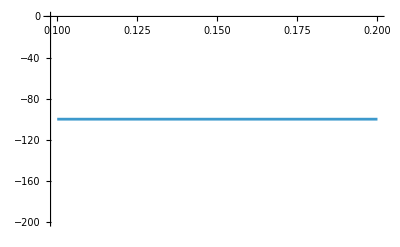

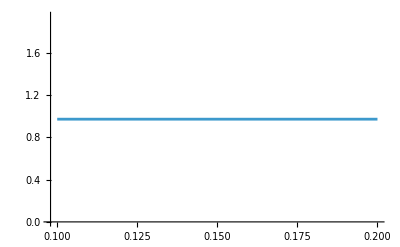

```mathematica
list={{0.1,8.428628244490481*^-9,9.715102602962144*^-8,1.0557965427411192*^-7},{0.11,8.428628090993513*^-9,9.715102577824199*^-8,1.055796538692355*^-7},{0.12000000000000001,8.428627993777687*^-9,9.715102561903344*^-8,1.0557965361281113*^-7},{0.13,8.428627929797585*^-9,9.715102551425426*^-8,1.0557965344405184*^-7},{0.14,8.428627886303518*^-9,9.715102544302473*^-8,1.0557965332932824*^-7},{0.15000000000000002,8.428627855904336*^-9,9.715102539324064*^-8,1.0557965324914497*^-7},{0.16,8.42862783414123*^-9,9.71510253575995*^-8,1.0557965319174074*^-7},{0.17,8.428627818230365*^-9,9.715102533154249*^-8,1.0557965314977285*^-7},{0.18,8.428627806380816*^-9,9.715102531213678*^-8,1.055796531185176*^-7},{0.19,8.428627797409697*^-9,9.715102529744486*^-8,1.0557965309485456*^-7},{0.2,8.42862779051724*^-9,9.715102528615721*^-8,1.0557965307667445*^-7}};
len=Length[list];
dat01=Table[{list[[i,1]],(Re[list[[i,2]]]/x[[2]]-1 )10^2},{i,1,len}]
dat02=Table[{list[[i,1]],(Re[list[[i,3]]])10^7},{i,1,len}];
ListLinePlot[dat01]
ListLinePlot[dat02]
```

```mathematica
mu=10.0^-1;v0val= 6 10^-4;in=1;rat=0.5;
x=Quiet[sig0[mu,v0val,{in,in,rat in}]]
list=Sort[Join[{x},Table[Quiet[sig[B,mu,v0val,{in,in,rat in}]],{B,-105,105,10}]]]
```

{0,7.93269×10^-9,3.67788×10^-8,4.47115×10^-8}

```mathematica
list=;len=Length[list];
{x1,x2}={1/7.932692307692297*^-9,1/3.6778846153846116*^-8};
dat11=Table[{list[[i,1]],(Re[list[[i,2]]]x1 -1)10^4},{i,1,len}];
dat12=Table[{list[[i,1]],(Re[list[[i,3]]]x2-1)10^6},{i,1,len}];
ListLinePlot[dat11];
ListLinePlot[dat12];
```

```mathematica
mu=10.0^-1;v0val= 6 10^-4;in=1;rat=1;
x=Quiet[sig0[mu,v0val,{in,in,rat in}]]
```

{0,7.03125×10^-9,2.10937×10^-8,2.8125×10^-8}

```mathematica
list={{-105,7.032400256636806*^-9,2.1093621338853858*^-8,2.8126021595490665*^-8},{-95,7.0321915895388226*^-9,2.1093644695824592*^-8,2.8125836285363415*^-8},{-85,7.03200379057587*^-9,2.1093665710624517*^-8,2.8125669501200387*^-8},{-75,7.031836859298207*^-9,2.1093684385298713*^-8,2.812552124459692*^-8},{-65,7.0316907953058795*^-9,2.1093700721664577*^-8,2.8125391516970457*^-8},{-55,7.031565598248786*^-9,2.109371472131204*^-8,2.8125280319560827*^-8},{-45,7.0314612678267315*^-9,2.10937263856037*^-8,2.8125187653430434*^-8},{-35,7.031377803789478*^-9,2.1093735715674858*^-8,2.8125113519464338*^-8},{-25,7.0313152059367925*^-9,2.1093742712433702*^-8,2.8125057918370496*^-8},{-15,7.031273474118463*^-9,2.109374737656126*^-8,2.8125020850679724*^-8},{-5,7.0312526082343345*^-9,2.1093749708511538*^-8,2.8125002316745872*^-8},{0,7.031249999999994*^-9,2.1093749999999977*^-8,2.812499999999997*^-8},{5,7.0312526082343395*^-9,2.1093749708511524*^-8,2.8125002316745862*^-8},{15,7.0312734741184605*^-9,2.109374737656126*^-8,2.812502085067972*^-8},{25,7.0313152059367925*^-9,2.1093742712433702*^-8,2.8125057918370496*^-8},{35,7.031377803789479*^-9,2.1093735715674858*^-8,2.8125113519464338*^-8},{45,7.031461267826734*^-9,2.1093726385603705*^-8,2.8125187653430437*^-8},{55,7.031565598248788*^-9,2.1093714721312047*^-8,2.8125280319560833*^-8},{65,7.0316907953058795*^-9,2.1093700721664567*^-8,2.8125391516970447*^-8},{75,7.031836859298209*^-9,2.109368438529872*^-8,2.812552124459693*^-8},{85,7.03200379057587*^-9,2.1093665710624524*^-8,2.8125669501200393*^-8},{95,7.032191589538824*^-9,2.1093644695824592*^-8,2.8125836285363415*^-8},{105,7.032400256636805*^-9,2.1093621338853848*^-8,2.812602159549065*^-8}};
len=Length[list];
{x1,x2}={1/7.031249999999994*^-9,1/2.1093749999999977*^-8};
dat21=Table[{list[[i,1]],(Re[list[[i,2]]]x1 -1)10^4},{i,1,len}];
dat22=Table[{list[[i,1]],(Re[list[[i,3]]]x2-1)10^6},{i,1,len}];
ListLinePlot[dat21];
ListLinePlot[dat22];
```

```mathematica
mu=10.0^-1;v0val= 6 10^-4;in=1;rat=2;
x=Quiet[sig0[mu,v0val,{in,in,rat in}]]
```

{0,5.65476×10^-9,1.16071×10^-8,1.72619×10^-8}

```mathematica
list={{-105,5.655556703410506*^-9,1.1606993541175754*^-8,1.726255024458626*^-8},{-95,5.655412518207785*^-9,1.1607020637801798*^-8,1.726243315600958*^-8},{-85,5.655282753056704*^-9,1.1607045021039756*^-8,1.726232777409646*^-8},{-75,5.655167407473868*^-9,1.160706669206651*^-8,1.7262234099540378*^-8},{-65,5.655066481029484*^-9,1.1607085651927947*^-8,1.7262152132957433*^-8},{-55,5.654979973347405*^-9,1.1607101901539043*^-8,1.7262081874886446*^-8},{-45,5.654907884105144*^-9,1.160711544168393*^-8,1.7262023325789075*^-8},{-35,5.654850213033931*^-9,1.160712627301595*^-8,1.726197648604988*^-8},{-25,5.654806959918711*^-9,1.1607134396057732*^-8,1.7261941355976442*^-8},{-15,5.654778124598188*^-9,1.1607139811201201*^-8,1.726191793579939*^-8},{-5,5.654763706964815*^-9,1.1607142518707614*^-8,1.726190622567243*^-8},{0,5.654761904761898*^-9,1.1607142857142846*^-8,1.7261904761904745*^-8},{5,5.654763706964814*^-9,1.1607142518707616*^-8,1.726190622567243*^-8},{15,5.654778124598188*^-9,1.1607139811201201*^-8,1.726191793579939*^-8},{25,5.6548069599187125*^-9,1.160713439605773*^-8,1.7261941355976442*^-8},{35,5.654850213033928*^-9,1.1607126273015949*^-8,1.7261976486049877*^-8},{45,5.654907884105144*^-9,1.1607115441683937*^-8,1.726202332578908*^-8},{55,5.654979973347402*^-9,1.1607101901539041*^-8,1.7262081874886443*^-8},{65,5.655066481029486*^-9,1.1607085651927947*^-8,1.7262152132957433*^-8},{75,5.655167407473868*^-9,1.160706669206651*^-8,1.7262234099540378*^-8},{85,5.655282753056702*^-9,1.1607045021039756*^-8,1.7262327774096457*^-8},{95,5.655412518207783*^-9,1.16070206378018*^-8,1.726243315600958*^-8},{105,5.655556703410504*^-9,1.1606993541175751*^-8,1.7262550244586255*^-8}};
len=Length[list];
{x1,x2}={1/5.654761904761898*^-9,1/1.1607142857142846*^-8};
dat31=Table[{list[[i,1]],(Re[list[[i,2]]]x1 -1)10^4},{i,1,len}];
dat32=Table[{list[[i,1]],(Re[list[[i,3]]]x2-1)10^6},{i,1,len}];
ListLinePlot[dat31];
ListLinePlot[dat32];
```

## Plots

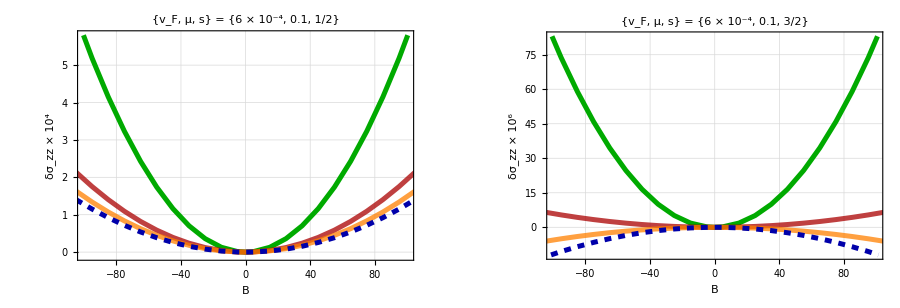

```mathematica
style={(**)Directive[Darker[Green],Thickness[0.008]],(**)Directive[Darker[Red],Thickness[0.008],Opacity[0.75]],(**)Directive[Orange,Thickness[0.008],Opacity[0.75]](*********),(**)Directive[Darker[Blue],Thickness[0.008],Dashed]};

g1=ListPlot[{dat01,dat11,dat21,dat31},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16],PlotRange->{{-100,100},{-0.1,5.8}},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,Axes->False,FrameLabel->{"B","δσ_zz × 10^4"},FrameTicksStyle->Directive[Bold,Black,12],PlotLabel->Style["{v_F, μ, s} = {6 × 10^-4, 0.1, 1/2}",Bold,Darker[Brown],18,FontFamily->"Times"],ImageSize->450,GridLines->Automatic];

g2=ListPlot[{dat02,dat12,dat22,dat32},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16],PlotRange->{{-100,100},{-12,83}},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,Axes->False,FrameLabel->{"B","δσ_zz × 10^6"},FrameTicksStyle->Directive[Bold,Black,12],PlotLabel->Style["{v_F, μ, s} = {6 × 10^-4, 0.1, 3/2}",Bold,Darker[Brown],18,FontFamily->"Times"],ImageSize->450,GridLines->Automatic];

leg=LineLegend[style,{"{1, 1, 0.1}", "{1, 1, 0.5}", "{1, 1, 1}", "{1, 1, 2}"},LabelStyle->{18,Darker[Brown],Bold,FontFamily->"Times"},LegendLayout->{"Row",1}];

pl=Legended[GraphicsGrid[{{g1,g2}},Spacings->{40,0},ImageSize->900],Placed[leg,Below]]
SetDirectory[NotebookDirectory[]];
Export["allwithomm.pdf",Rasterize[pl],ImageResolution->1000];
```

## trials

{0,8.42863×10^-7,9.7151×10^-6,0.000010558}

{{-35,1.4397×10^-6,0.000010602,0.0000120417},{-25,1.14801×10^-6,0.0000101927,0.0000113407},{-15,9.52221×10^-7,9.89144×10^-6,0.0000108437},{-5,8.54974×10^-7,9.7349×10^-6,0.0000105899},{0,8.42863×10^-7,9.7151×10^-6,0.000010558},{5,8.54974×10^-7,9.7349×10^-6,0.0000105899},{15,9.52221×10^-7,9.89144×10^-6,0.0000108437},{25,1.14801×10^-6,0.0000101927,0.0000113407},{35,1.4397×10^-6,0.000010602,0.0000120417}}

{1.18643×10^6,102933.}

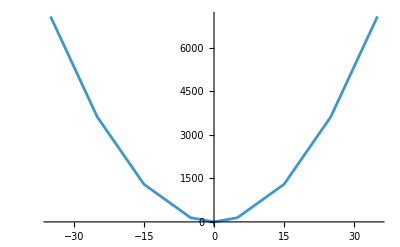

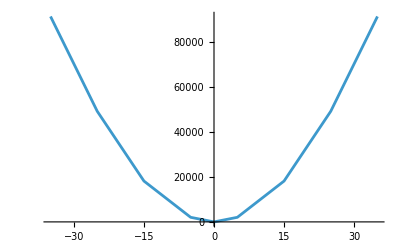

```mathematica
mu=10.0^-1;v0val= 6 10^-3;in=1;rat=0.1;
x=Quiet[sig0[mu,v0val,{in,in,rat in}]]
list=Sort[Join[{x},Table[Quiet[sig[B,mu,v0val,{in,in,rat in}]],{B,-35,35,10}]]]
len=Length[list];
{x1,x2}={1/x[[2]],1/x[[3]]}
dat31=Table[{list[[i,1]],(Re[list[[i,2]]]x1 -1)10^4},{i,1,len}];
dat32=Table[{list[[i,1]],(Re[list[[i,3]]]x2-1)10^6},{i,1,len}];
ListLinePlot[dat31]
ListLinePlot[dat32]
```

{0,5.65476×10^-7,1.16071×10^-6,1.72619×10^-6}

{{-35,6.54847×10^-7,1.13197×10^-6,1.78682×10^-6},{-25,6.1119×10^-7,1.14971×10^-6,1.7609×10^-6},{-15,5.81801×10^-7,1.15738×10^-6,1.73918×10^-6},{-5,5.6728×10^-7,1.16037×10^-6,1.72765×10^-6},{0,5.65476×10^-7,1.16071×10^-6,1.72619×10^-6},{5,5.6728×10^-7,1.16037×10^-6,1.72765×10^-6},{15,5.81801×10^-7,1.15738×10^-6,1.73918×10^-6},{25,6.1119×10^-7,1.14971×10^-6,1.7609×10^-6},{35,6.54847×10^-7,1.13197×10^-6,1.78682×10^-6}}

{1.76842×10^6,861538.}

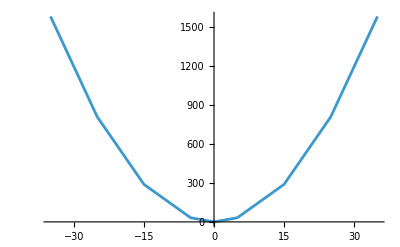

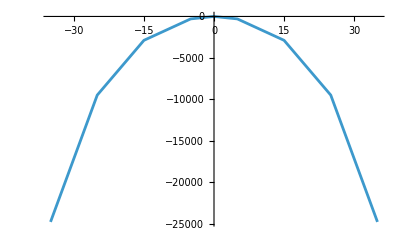

```mathematica
mu=10.0^-1;v0val= 6 10^-3;in=1;rat=2;
x=Quiet[sig0[mu,v0val,{in,in,rat in}]]
list=Sort[Join[{x},Table[Quiet[sig[B,mu,v0val,{in,in,rat in}]],{B,-35,35,10}]]]
len=Length[list];
{x1,x2}={1/x[[2]],1/x[[3]]}
dat31=Table[{list[[i,1]],(Re[list[[i,2]]]x1 -1)10^4},{i,1,len}];
dat32=Table[{list[[i,1]],(Re[list[[i,3]]]x2-1)10^6},{i,1,len}];
ListLinePlot[dat31]
ListLinePlot[dat32]
```